```mathematica
ClearAll["Global`*"]
(*~ MacOS ~*)
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/scratch/testing";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
$Line=0;
```

```mathematica
main="/Users/mikhailgaerlan/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/scratch/testing";
(*~ Windows ~*)
(*main="/Users/Mikhail/Box Sync/Education/MSU/2015-2016 Fall/PH 4433 Computational Physics/Homework/Homework 4/ohg6-hw4/";*)

SetDirectory[main];
```

```mathematica
data=Table[Import["data/data_3_"<>IntegerString[i,10,3]<>".txt","Data"],{i,1,100,1}];
```

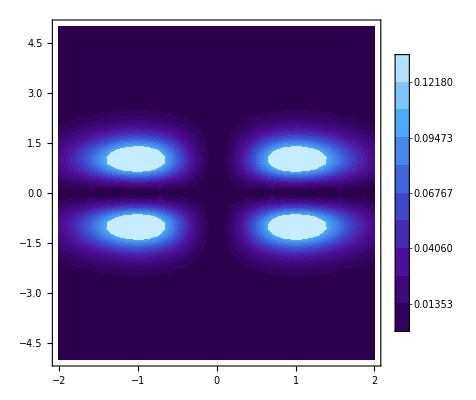

```mathematica
contour=ContourPlot[x^2 y^2 Exp[-(x^2+y^2)],{x,-2,2},{y,-5,5},ColorFunction->(ColorData["DeepSeaColors"][#]&),Contours->20,ContourStyle->None,PlotLegends->Table[i,{i,0,Exp[-2],Exp[-2]/10}]]
```

```mathematica
begin=1;end=100;steps=5;subdata=data[[Table[i,{i,begin,end,steps}],All,{2,3}]];
```

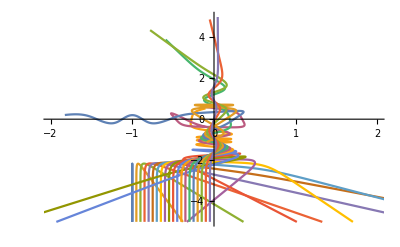

```mathematica
lines=ListLinePlot[subdata,PlotRange->{{-2,2},{-5,5}}]
```

```mathematica
Export["testing.gif",Table[Show[contour,lines,ListPlot[Table[{subdata[[i,x]]},{i,1,20}]]],{x,1,Length[subdata[[1]]],60}],"DisplayDurations"->1/5]
```

testing.gif